# Penrose Encoding and graph visualization.

## Diana Itzel Vázquez Santiago Emmanuel Isaac Juárez Caballero Jesús Eduardo Hermosilla Díaz. Maestría en Inteligencia Artificial, generación 2021-2023

## Initializing Cells

```mathematica
(*Starting Executing Cells*)
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
FindExternalEvaluators["Python"]
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

## Execution of the python code for the penrose Encoding.

```mathematica
NotebookDirectory[]
```

C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\

```mathematica
FileNames["*","C:\\Users\\emman\\OneDrive\\Documentos\\GitHub\\PenroseEncodingFinalProyect\\"]
```

{C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.git,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.gitattributes,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\LICENSE,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\nuniversal.txt,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\penrose_encoding.py,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\README.md,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\Turing.nb}

```mathematica
u=Import["nuniversal.txt"]//ToExpression;
n=u;
ExternalEvaluate[session,File["penrose_encoding.py"]];
PenroseEncoding=ExternalEvaluate[session,"codificacion"];
execution=PenroseEncoding[n];
```

TM after Penrose Coding:  R100000001L10R10010111R100R100110000R110R10011101R1000R10011011R1010L10110101L1100L11101011L1110R100110011R10000R101000011R10010L101100011L10100L101110001L10110R10001000L11000L110001010L100111R11011R10000R11101R1010100R10000000R100000L1101111L100010L101111111L1000111L100011001L100110R101000110R1011010R101001R11001L101011L101100L11011010L1111000R101111L1101001R110001R110010R11111001R101110101R110101L111011L110110R111000L100101011L111011L1110000L11010000R111101L11011R10010100L1000000L101101111L101101011L1000011L1000100L100001110L1000110L100001001L1001000L100010110L10010001R1001101L1001101R10100001R100111010R1001111L1010000L10101111L11110R1010011R1010101R10000001R10000100R10000101R100000000R1011001L1011100R1011011R1000010L1011101R1010L110000011L1100000R11100111R10111R1100011L1101011L1100101R11010001L100000L1101001R110110R111001L1101101L11100001L11100001L100000L11100011L10111R1110001L1100111L1110101L1111000L11000000L10101000R10101001R111110L100000001R101000R1111101L101000R10100111L1000100L1001000L1000R10000001R10000101L1110111R100100101L1000010L1110R10000111R10001000L101000100L1111110L10001010L100101000L10001101R100011000L111111L1001010R1001010R1101101L10010011L1000000L10010101L10R101010001R11110R10011001L1000R110001001R110R11101101R1110R101011L10R10100001R100111100L10100011R10000010R10100101L101000R110000101L1010110R1010111R10R10101101R10R101100001R1010000L11010R11110001L10110001L101111L1100101R1010L10111001L10010L110001R1010L1011111L10100L10111101L10100L110000111L0R1100001R1010L11000001L101R11000011R101101L11000101L1000R110010001R110R11001001R111101L11001101R1001111L10100011R11001L11010111L1110101L1100L1100L11010101L1100L11011001L11001L11000101L1100L10011001L101101L11011101L10111111R110001111R100010L100011111L1110011L1110011L100000L11100101L100000L11101001L1100000R110001R100000L101000001L1100L11010011L110R11110011R10000R11110111R10000010R1111010L110R11110101R110R101010L10000R11111011R110010R100110111L10000R11111101R100100L100111111R100100L100011L100101000L10R100000010L100000101L100100110L100000101L101111101R10001111L100101101L100001001L11101R10010010L100001011L100000111R1000100L0H100010000L10001010L100001101L100001101R100010011L100010010R1001000L1H100010101L100010101L100000011L100011100R100101L100010000L100010L100100001L11101R100100001L10001111L100000111L100100011L100100011L1010000L1101010R10000011L100100101L111000L11011R101111000R10000110R1000000L100001010L101R101001101R1110R100110101R1110R100111001R0R110101L1110R10011111R0R1100111R0R101001111L100100L101011111R101101100R101000001L10000R11101111R10111R101001001L100111R11000011R10010000R1010011R100010L11011111L101R101010011R0R101010111L10R10101011R101R101010101R101R101011001R0R101011011L10011L10101L0R101011101L0R101100111L100100L10001101R1011001L10110011R10010L101100101L10010L101101001L0R10100100L10010L10110111L0R10110000L0R11111R1000000L101110111L10100L10111011L0R100011010R0R110000R1000000L101111011L0R11001000R1000000L100101111L100100L11111111R100010L101001011L101110010R110000001R1010L1100011L101000R110000001R10100L110101L1000R11000111R11001L110001101L11001L11001111L0R110011R1000R11001011R

Instructions from TM

0                 00 -> 00R

1          01 -> 100000001L

2                 10 -> 10R

3           11 -> 10010111R

4               100 -> 100R

..                      ...

397  110001101 -> 11001111L

398         110001110 -> 0R

399    110001111 -> 110011R

400      110010000 -> 1000R

401  110010001 -> 11001011R

[402 rows x 1 columns]

## Pre-processing rules for the instructions that came from Penrose Encoding

```mathematica
MT=Import["universal.txt"];
```

```mathematica
MT=StringDelete[StringSplit[Text[MT]⟦1⟧,","],{"[","]","'", " "}];
```

## Visualization using Multigraph2 with modified elements (originally taken from: https://mathematica.stackexchange.com/questions/201183/how-to-get-distinct-labels-on-parallel-edges-in-a-graph)

### MultiGraph2 implementation: A tool to visualize correctly multilabel graphs on Wolfram Mathematica

```mathematica
ClearAll[multiGraph2]
multiGraph2[vl_,elist_,elabels_,estyles_,o:OptionsPattern[Graph]]:=Module[{esf,edges,labels,styles,sorted=Transpose@SortBy[Transpose[{elist,elabels,estyles}],{PositionIndex[vl]@#[[1,1]]&,PositionIndex[vl]@#[[1,2]]&}]},{edges,labels,styles}={sorted[[1]],##&@@(RotateRight/@sorted[[2;;]])};
esf={First[styles=RotateLeft[styles]],GraphElementData["Arrow", "ArrowSize"->0.01][##]/. Arrowheads[ah_]:>Arrowheads[Append[ah,{.0003,.7,Graphics[Text[Framed[First[labels=RotateLeft[labels]],FrameStyle->None,Background->White]]]}]]}&;
Graph[vl,edges,EdgeShapeFunction->esf,o]]
```

### Table generation for associations in the graph in order to be functional with multigraph2

```mathematica
fn=ParallelTable[{{FromDigits[(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ,2]},{FromDigits[((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ),2]->FromDigits[((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin),2]},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

### Visualization of the graph using Gravity Embedding, a method to visualize more clearly the graph.

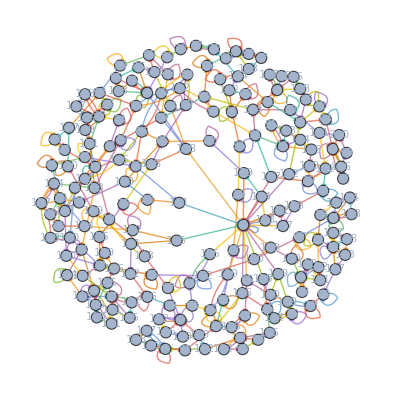

```mathematica
styles=ColorData[97]/@Range[Length[fn[[;;,3]]]];
multiGraph2[Flatten@Gather[(fn[[;;,1]]//Flatten)//DeleteDuplicates],fn[[;;,2]]//Flatten,fn[[;;,3]]//Flatten,styles,VertexSize->1,VertexLabels->Placed["Name",Center],ImageSize->Full, GraphLayout->"GravityEmbedding"]
```

## Past implementation (delete this at the end)

```mathematica
tabla3=ParallelTable[{{(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin },{((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin )->((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin)},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```